```mathematica
dir="D:\\workingBuffer 2";
```

```mathematica
dir="D:\\big";
```

```mathematica
indexOfEgg=6;
```

```mathematica
GetNumberOfOrganisms[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nFertile},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms="o"/.items//CountDistinct;
nFertile=Cases[{"o","ct"}/.items,{x_,indexOfEgg}->x]//CountDistinct;
{nOrganisms,nFertile}
]
```

```mathematica
GetCellsPerOrganism[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nCells},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms="o"/.items//CountDistinct;
nCells =items//Length;
nCells/nOrganisms
]
```

```mathematica
f0=0;
fMax=2000000;
df=10000;
GetNumberOfOrganisms[fMax]//Print;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames]//Transpose;
```

{236,223}

Import::nffil: File not found during Import.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

MapThread::mptd: Object First[$Failed] at position {2, 1} in MapThread[#1→#2&,{First[$Failed],$Failed}] has only 0 of required 1 dimensions.

MapThread::argtu: MapThread called with 1 argument; 2 or 3 arguments are expected.

ReplaceAll::reps: {MapThread[{First[$Failed],$Failed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

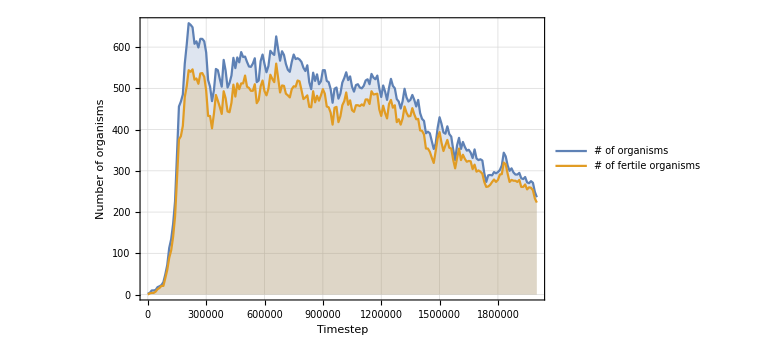

```mathematica
plot=ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
PlotLegends->Placed[{"# of organisms","# of fertile organisms"},Above],
ImageSize->Large,
GridLines->Automatic
]
```

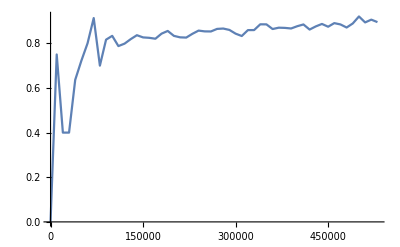

```mathematica
ListLinePlot[(#⟦2⟧)/(#⟦1⟧)&/@Transpose[nOrgsList],DataRange->{f0,fMax}]
```

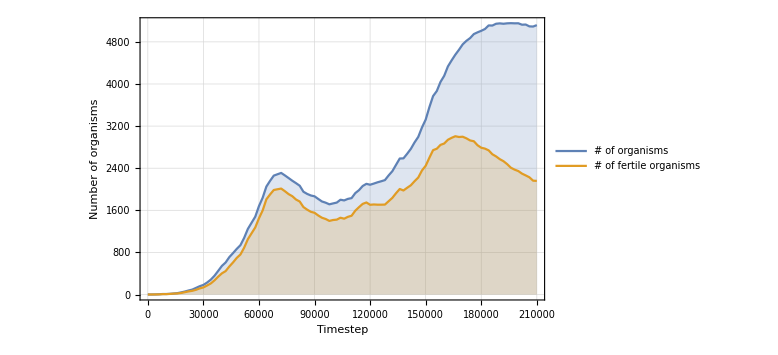

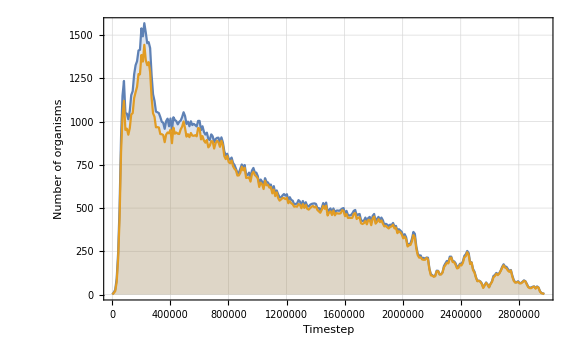

```mathematica
cellFreqList=ParallelMap[GetCellsPerOrganism,frames];
```

Import::nffil: File not found during Import.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

MapThread::mptd: Object First[$Failed] at position {2, 1} in MapThread[#1→#2&,{First[$Failed],$Failed}] has only 0 of required 1 dimensions.

MapThread::argtu: MapThread called with 1 argument; 2 or 3 arguments are expected.

ReplaceAll::reps: {MapThread[{First[$Failed],$Failed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

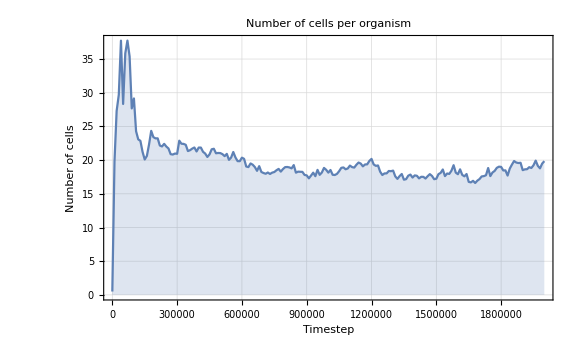

```mathematica
plot2=ListPlot[
cellFreqList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
PlotLabel->"Number of cells per organism",
FrameLabel->{"Timestep","Number of cells"},
ImageSize->Large,
GridLines->Automatic
]
```